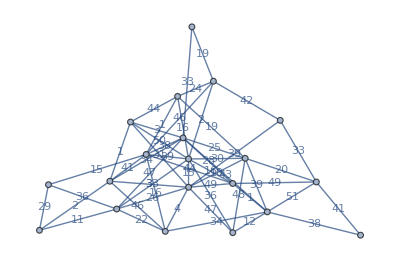

```mathematica
g=Graph[RandomGraph[{20,54}],EdgeCost->RandomInteger[{-54,54},54],EdgeWeight->RandomInteger[54,54],EdgeLabels->"EdgeWeight"]
```

```mathematica
FindMinimumCostFlow[g,1,3]
```

2

```mathematica
EvenMixedGraphAlgorithm[g_?MixedGraphQ]:=Block[{arcs,edges},arcs=EdgeList[g,_->_];edges=EdgeList[g,_<->_];]
```

```mathematica
EdgeList[g],RandomInteger[EdgeCount[g]]
```

{12<->16,7<->18,10<->14,7<->13,2<->14,19<->20,7<->16,1<->3,6<->18,6<->19}

```mathematica
?"*Replace*"
```

```mathematica
DirectedEdge[a<->b]
```

DirectedEdge[a<->b]

```mathematica
First[a<->b]
```

a

```mathematica
EdgeList[g]/.BlockRandom@RandomChoice[{a_<->b_:>a->b,a_<->b_:>a<->b}]
```

{1<->3,1<->11,2<->6,2<->11,2<->13,2<->14,2<->15,2<->16,3<->4,3<->5,3<->6,3<->16,4<->13,4<->14,5<->6,5<->9,5<->16,5<->17,6<->11,6<->16,6<->18,6<->19,6<->20,7<->8,7<->11,7<->13,7<->16,7<->18,7<->19,8<->18,8<->20,9<->11,9<->12,9<->13,9<->14,9<->15,9<->16,10<->14,10<->15,11<->15,11<->17,11<->20,12<->13,12<->15,12<->16,13<->16,13<->17,13<->19,13<->20,14<->15,15<->19,16<->17,17<->20,19<->20}

```mathematica
MapAt[(First[#]->Last[#])&,EdgeList[g],RandomInteger[{1,54},4]]
```

MapAt::partw: Part {31,24,10,43} of {1<->3,1<->11,2<->6,2<->11,2<->13,2<->14,2<->15,2<->16,3<->4,3<->5,«44»} does not exist.

MapAt[First[#1]->Last[#1]&,{1<->3,1<->11,2<->6,2<->11,2<->13,2<->14,2<->15,2<->16,3<->4,3<->5,3<->6,3<->16,4<->13,4<->14,5<->6,5<->9,5<->16,5<->17,6<->11,6<->16,6<->18,6<->19,6<->20,7<->8,7<->11,7<->13,7<->16,7<->18,7<->19,8<->18,8<->20,9<->11,9<->12,9<->13,9<->14,9<->15,9<->16,10<->14,10<->15,11<->15,11<->17,11<->20,12<->13,12<->15,12<->16,13<->16,13<->17,13<->19,13<->20,14<->15,15<->19,16<->17,17<->20,19<->20},{31,24,10,43}]

```mathematica
MapAt[(First[#]->Last[#])&,{a<->b,b<->c,c<->d,d<->a},List/@BlockRandom[RandomInteger[{2,3},2]]]
```

{a<->b,b->c,c<->d,d<->a}